```mathematica
<<"/Users/lucaarnaboldi/Desktop/staircase-ss/mathematica/Isserlis.m"
```

```mathematica
Omega
```

{{ω[1,1],ω[1,2],ω[1,3],ω[1,4],ω[1,5],ω[1,6],0},{ω[1,2],ω[2,2],ω[2,3],ω[2,4],ω[2,5],ω[2,6],0},{ω[1,3],ω[2,3],ω[3,3],ω[3,4],ω[3,5],ω[3,6],0},{ω[1,4],ω[2,4],ω[3,4],ω[4,4],ω[4,5],ω[4,6],0},{ω[1,5],ω[2,5],ω[3,5],ω[4,5],ω[5,5],ω[5,6],0},{ω[1,6],ω[2,6],ω[3,6],ω[4,6],ω[5,6],ω[6,6],0},{0,0,0,0,0,0,Δ}}

```mathematica
(*l = 1*)
(*I2noise = Expand[1]
I2 = Expand[(lf[1])*(lf[2])]
I3 = Expand[(1)*lf[2]*(lf[3])]
I4 = Expand[(1)*(1)*(lf[3])*(lf[4])]*)

(*l=2*)
(*I2noise = Expand[(2*lf[1])*(2*lf[2])]
I2 = Expand[(lf[1]^2-1)*(lf[2]^2-1)]
I3 = Expand[2*lf[1]*lf[2]*(lf[3]^2-1)]
I4 = Expand[(2*lf[1])*(2*lf[2])*(lf[3]^2-1)*(lf[4]^2-1)]*)

(*l=3*)
I2noise = Expand[(3*lf[1]^2-3)*(3*lf[2]^2-3)]
I2 = Expand[(lf[1]^3-3*lf[1])*(lf[2]^3-3*lf[2])]
I3 = Expand[(3*lf[1]^2-3)*lf[2]*(lf[3]^3-3*lf[3])]
I4 = Expand[(3*lf[1]^2-3)*(3*lf[2]^2-3)*(lf[3]^3-3*lf[3])*(lf[4]^3-3*lf[4])]

(*l=4*)
(*I2noise = Expand[(4*lf[1]^3-12*lf[1])*(4*lf[2]^3-12*lf[2])]
I2=Expand[(lf[1]^4-6*lf[1]^2+3)*(lf[2]^4-6*lf[2]^2+3)]
I3 = Expand[(4*lf[1]^3-12*lf[1])*lf[2]*(lf[3]^4-6*lf[3]^2+3)]
I4 = Expand[(4*lf[1]^3-12*lf[1])*(4*lf[2]^3-12*lf[2])*(lf[3]^4-6*lf[3]^2+3)*(lf[4]^4-6*lf[4]^2+3)]*)

(*l=5*)
(*I3 = Expand[(5*lf[1]^4-30*lf[1]^2+15)*lf[2]*(lf[3]^5-10*lf[3]^3+15*lf[3])]*)
(*I4 = Expand[(5*lf[1]^4-30*lf[1]^2+15)*(5*lf[2]^4-30*lf[2]^2+15)*(lf[3]^5-10*lf[3]^3+15*lf[3])*(lf[4]^5-10*lf[4]^3+15*lf[4])]*)

(*l=6*)
(*I3 = Expand[(6*lf[1]^5-60*lf[1]^3+90*lf[1])*lf[2]*(lf[3]^6-15*lf[3]^4+45*lf[3]^2-15)]*)
(*I4 = Expand[(6*lf[1]^5-60*lf[1]^3+90*lf[1])*(6*lf[2]^5-60*lf[2]^3+90*lf[2])*(lf[3]^6-15*lf[3]^4+45*lf[3]^2-15)*(lf[4]^6-15*lf[4]^4+45*lf[4]^2-15)]*)
```

9-9 λ[1]^2-9 λ[2]^2+9 λ[1]^2 λ[2]^2

9 λ[1] λ[2]-3 λ[1]^3 λ[2]-3 λ[1] λ[2]^3+λ[1]^3 λ[2]^3

9 λ[2] λ[3]-9 λ[1]^2 λ[2] λ[3]-3 λ[2] λ[3]^3+3 λ[1]^2 λ[2] λ[3]^3

81 λ[3] λ[4]-81 λ[1]^2 λ[3] λ[4]-81 λ[2]^2 λ[3] λ[4]+81 λ[1]^2 λ[2]^2 λ[3] λ[4]-27 λ[3]^3 λ[4]+27 λ[1]^2 λ[3]^3 λ[4]+27 λ[2]^2 λ[3]^3 λ[4]-27 λ[1]^2 λ[2]^2 λ[3]^3 λ[4]-27 λ[3] λ[4]^3+27 λ[1]^2 λ[3] λ[4]^3+27 λ[2]^2 λ[3] λ[4]^3-27 λ[1]^2 λ[2]^2 λ[3] λ[4]^3+9 λ[3]^3 λ[4]^3-9 λ[1]^2 λ[3]^3 λ[4]^3-9 λ[2]^2 λ[3]^3 λ[4]^3+9 λ[1]^2 λ[2]^2 λ[3]^3 λ[4]^3

```mathematica
Psit =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->m,ω[2,2]->ρ,ω[2,3]->ρ,ω[3,3]->ρ} ;
Psis= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->q,ω[2,2]->ρ,ω[2,3]->m,ω[3,3]->q} ;
(*Psis = 0;*)
PhiHDtt = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[1,4]->m,ω[2,2]->q,ω[2,3]->m,ω[2,4]->m,ω[3,3]->ρ,ω[3,4]->ρ,ω[4,4]->ρ} ;
PhiHDss = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->q,ω[2,2]->q,ω[2,3]->q,ω[2,4]->q,ω[3,3]->q,ω[3,4]->q,ω[4,4]->q} ;
(*PhiHDss = 0;*)
PhiHDts = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->m,ω[2,2]->q,ω[2,3]->q,ω[2,4]->m,ω[3,3]->q,ω[3,4]->m,ω[4,4]->ρ} ;
(*PhiHDts = 0;*)
PhiHDnoise = IsserlisTheorem[I2noise] /. {ω[1,1]->q,ω[1,2]->m,ω[2,2]->ρ};
PhiGFt =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[2,2]->q,ω[2,3]->m,ω[3,3]->ρ} ;
PhiGFs= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[2,2]->q,ω[2,3]->q,ω[3,3]->q} ;
(*PhiGFs=0;*)
Riskss =IsserlisTheorem[I2] /.{ω[1,1]->q,ω[1,2]->q,ω[2,2]->q};
(*Riskss = 0;*)
Risktt = IsserlisTheorem[I2] /.{ω[1,1]->ρ,ω[1,2]->ρ,ω[2,2]->ρ};
Riskts = IsserlisTheorem[I2] /.{ω[1,1]->q,ω[1,2]->m,ω[2,2]->ρ};
(*Riskts = 0;*)
Pinv = 1/ρ;
Qorthinv = 1/(q-m^2/ρ);
GFM = FullSimplify[(Psit-Psis)];
GFQ = FullSimplify[(PhiGFt-PhiGFs)];
GFQorth = FullSimplify[GFQ - m*Pinv*GFM];
HDQ = (PhiHDtt+PhiHDss-2*PhiHDts+Δ*PhiHDnoise);
mUpdate =γ*GFM
qUpdate = FullSimplify[2*γ*GFQ+γ^2*1/α*HDQ+γ^2*ind*(GFM*Pinv*GFM)+γ^2*ind*(GFQorth*Qorthinv*GFQorth)]
PopRisk = 1/2*(Riskss +Risktt-2*Riskts)
```

9 γ (m (-1+(4-5 q) q)+(-1+q) (-1+ρ) ρ+m^2 (-2+4 ρ))

1/α 9 γ (-120 q^4 (7+3 ind α) γ+45 q^5 (21+5 ind α) γ+2 q^3 (-5 α+3 (55+39 ind α) γ)+4 m^3 (α-3 (7+3 ind α+15 q^2 (7+ind α)-2 q (25+6 ind α)) γ)-2 m (9 (-1+q (7+5 q (-5+7 q))) γ+(-1+3 q) α (-1+9 ind (1+q (-4+5 q)) γ)) (-1+ρ)+36 m^4 γ (-4+10 ρ+ind α (-2+3 ρ))+γ (Δ-Δ ρ+3 ρ (3+3 ind α (-1+ρ)^2+ρ (-6+5 ρ)))+2 m^2 γ (-18+Δ+72 ρ-90 ρ^2-18 ind α (-1+ρ) (-1+2 ρ)+18 q (3+ind α (-1+ρ) (-2+3 ρ)+3 ρ (-4+5 ρ)))+q (α (-2+9 ind γ (1-2 (-1+ρ)^2 ρ))+γ (9+Δ (-1+ρ)-6 ρ (3+ρ (-6+5 ρ))))+q^2 (α (8+9 ind γ (-8+(-1+ρ)^2 ρ))+9 γ (-8+ρ (3+ρ (-6+5 ρ)))))

1/2 (9 q-18 q^2+15 q^3+9 ρ-18 ρ^2+15 ρ^3-2 (9 m+6 m^3-9 m q-9 m ρ+9 m q ρ))

```mathematica
mUpdateSpherical = Expand[FullSimplify[((m+mUpdate)/Sqrt[q+qUpdate])/.{ρ->1,q->1,ind->1,Δ->0,m->t*Sqrt[y],γ->y^(δ),α->y^(μ-1)}]]
```

(t √y)/(√(1+36 y^(δ-μ) (-186 t^3 y^(5/2+δ)+t^3 y^(3/2+μ)-18 t^3 y^(3/2+δ+μ)+6 y^(1+δ) (16+6 t^2 y+9 t^4 y^2)+y^μ (-1+9 y^δ (1+t^4 y^2)))))-(18 t y^(1/2+δ))/(√(1+36 y^(δ-μ) (-186 t^3 y^(5/2+δ)+t^3 y^(3/2+μ)-18 t^3 y^(3/2+δ+μ)+6 y^(1+δ) (16+6 t^2 y+9 t^4 y^2)+y^μ (-1+9 y^δ (1+t^4 y^2)))))+(18 t^2 y^(1+δ))/(√(1+36 y^(δ-μ) (-186 t^3 y^(5/2+δ)+t^3 y^(3/2+μ)-18 t^3 y^(3/2+δ+μ)+6 y^(1+δ) (16+6 t^2 y+9 t^4 y^2)+y^μ (-1+9 y^δ (1+t^4 y^2)))))

```mathematica
aroundInit = FullSimplify[Asymptotic[(mUpdateSpherical/Sqrt[y])/.{δ->3/2-1+ϵ,μ->2}, y->0]]
Assumptions[{ϵ∈Reals,y∈Reals,y>0},Solve[(t-18 t y^ϵ (√y))/(√(1-216 t^3 y^(3/2+2 ϵ) (31)))==t,t]]
```

(t-18 t y^ϵ (√y-t y))/(√(1-216 t^3 y^(3/2+2 ϵ) (31+3 y)))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Assumptions[{ϵ∈ℝ,y∈ℝ,y>0},{{t→0},{t→-(-1/186)^(1/3) (-9/(√y)+y^(-1-ϵ))^(1/3)},{t→((-9/(√y)+y^(-1-ϵ))^(1/3))/186^(1/3)},{t→((-1)^(2/3) (-9/(√y)+y^(-1-ϵ))^(1/3))/186^(1/3)}}]

0.1 x+0.9 x^2

1/2 (12-12 x^3)

-0.1 (-1/2+m^2/2)-0.9 (-1/3+m^3/3)

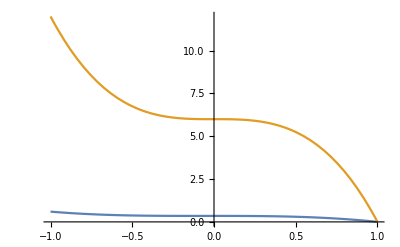

```mathematica
functionMUpdateSpherical[x_] = mUpdateSpherical /. {ρ->1,q->1,m->x, γ->.05,Δ->0, α->+Infinity}
functionPopRisk[x_] =PopRisk /.{ρ->1,q->1,m ->x,Δ->0}
EffectivePontentialSGD[m_]= -Integrate[functionMUpdateSpherical[x], {x,1,m}]
Plot[{EffectivePontentialSGD[m],functionPopRisk[m]},{m,-1,1}]
```

```mathematica
FortranForm[IsserlisTheorem[I3]/.{ω[1,1]->Caa,ω[1,2]->Cab, ω[1,3]->Cac,ω[1,4]->Cad,ω[2,2]->Cbb,ω[2,3]->Cbc, ω[2,4]->Cbd,ω[3,3]->Ccc,ω[3,4]->Ccd,ω[4,4]->Cdd}]
```

-18*Cab*Cac + 9*Cbc - 9*Caa*Cbc + 18*Cac**2*Cbc + 18*Cab*Cac*Ccc - 
     -  9*Cbc*Ccc + 9*Caa*Cbc*Ccc

```mathematica
FortranForm[mUpdateSpherical ]
```

m/Sqrt(1 + (18*γ*(192*γ + 
     -          2*α*(-1 + m**3 + 9*ind*(1 + (-2 + m)*m**3)*γ) + 
     -          m**2*γ*(72 + 12*m*(-31 + 9*m) + Δ)))/α) - 
     -  (18*m*γ)/
     -   Sqrt(1 + (18*γ*(192*γ + 
     -          2*α*(-1 + m**3 + 9*ind*(1 + (-2 + m)*m**3)*γ) + 
     -          m**2*γ*(72 + 12*m*(-31 + 9*m) + Δ)))/α) + 
     -  (18*m**2*γ)/
     -   Sqrt(1 + (18*γ*(192*γ + 
     -          2*α*(-1 + m**3 + 9*ind*(1 + (-2 + m)*m**3)*γ) + 
     -          m**2*γ*(72 + 12*m*(-31 + 9*m) + Δ)))/α)